### Nuclear FFs

#### Derive the helm form factors

```mathematica
FourierTransform[HeavisideTheta[R-r],r,q]
```

-(ⅈ ⅇ^(ⅈ q R))/(√(2 π) q)+√(π/2) DiracDelta[q]

```mathematica
FourierTransform[E^(-r^2/b^2)HeavisideTheta[R-r],r,q]
```

$Aborted

```mathematica
Integrate[r Sin[q r] ,{r,0,R}]
```

(-q R Cos[q R]+Sin[q R])/q^2

```mathematica
Integrate[r Sin[q r] E^(-r^2/b^2),{r,0,∞}]
```

ConditionalExpression[(ⅇ^(-1/4 b^2 q^2) √π q)/(4 (1/b^2)^(3/2)), Re[b^2]>0]

```mathematica
Integrate[r/((2 π s^2)^(3/2)) Sin[q r] E^(-r^2/s^2),{r,0,∞}]
```

ConditionalExpression[(ⅇ^(-1/4 q^2 s^2) q √(1/s^2) √(s^2))/(8 √2 π), Re[s^2]>0]

```mathematica
PowerExpand[Integrate[(4 π r)/(q(2 π s^2)^(3/2)) Sin[q r] E^(-r^2/s^2),{r,0,∞}]]
```

ConditionalExpression[(ⅇ^(-1/4 q^2 s^2))/(2 √2), Re[s^2]>0]

#### Corrected helm derivation following analytic nuclear scattering handbook

```mathematica
PowerExpand[Integrate[(4π r^2)/((2 π s^2)^(3/2))E^(-r^2/(2 s^2)),{r,0,∞}]]
```

ConditionalExpression[1, Re[s^2]>0]

Boom baby!

```mathematica
PowerExpand[Integrate[(4 π r)/q Sin[q r](E^(-r^2/(2 s^2)))/((2 π s^2)^(3/2)),{r,0,∞}]]
```

ConditionalExpression[ⅇ^(-1/2 q^2 s^2), Re[s^2]>0]

```mathematica
Integrate[3/(4π R^3)(4 π)/q r Sin[q r] ,{r,0,R}]
```

(3 (-q R Cos[q R]+Sin[q R]))/(q^3 R^3)

#### Plot the momentum space helm ff

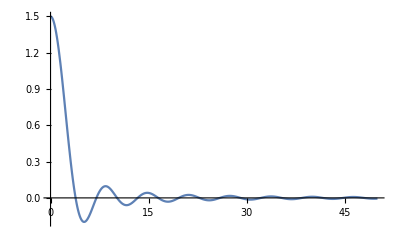

```mathematica
rn = 1;
Plot[3 BesselJ[1,q rn]/(q rn),{q,0,50},PlotRange->All]
```

and squared as would appear in a matrix element

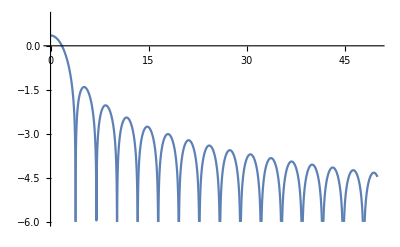

```mathematica
rn = 1;
Plot[Log10[(3 BesselJ[1,q rn]/(q rn))^2],{q,0,50},PlotRange->{-6,1}]
```

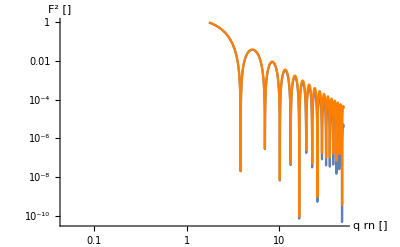

```mathematica
rn = 1;
s=0.03;
Show[{LogLogPlot[N[(3 BesselJ[1,q rn]/(q rn))^2 E^(-(q s)^2)],{q,0,50},PlotRange->{-6,1},AxesLabel->{"q rn []","F^2 []"}],LogLogPlot[N[(3 BesselJ[1,q rn]/(q rn))^2],{q,0,50},PlotRange->{-6,1},PlotStyle->Orange]}]
```

```mathematica
rnFe =1.14  A^(1/3) /.A->56 ; (* [fm] iron mass number parametrizaiton from analytic nuclear scattering handbook*)
rnSi =1.14  A^(1/3) /.A->28 ; (* [fm] silicon mass number parametrizaiton from analytic nuclear scattering handbook*)
rnMg =1.14  A^(1/3) /.A->24 ; (* [fm] magnesium mass number parametrizaiton from analytic nuclear scattering handbook*)
rnO =1.14  A^(1/3) /.A->16 ; (* [fm] oxygen mass number parametrizaiton from analytic nuclear scattering handbook*)
s=0.9 ; (*[fm] skin depth *)
Show[{LogPlot[Callout[N[(3 BesselJ[1,q rnFe]/(q rnFe))^2 E^(-(q s)^2)],"Fe",Below],{q,0,5 },PlotRange->{-6,3},AxesLabel->{"q[fm^-1]","Z^2(q) []"}],LogPlot[Callout[N[(3 BesselJ[1,q rnSi]/(q rnSi))^2 E^(-(q s)^2)],"Si"],{q,0,5 },PlotStyle->Orange],LogPlot[Callout[N[(3 BesselJ[1,q rnMg]/(q rnMg))^2 E^(-(q s)^2)],"Mg",Below],{q,0,5 },PlotStyle->Green],LogPlot[Callout[N[(3 BesselJ[1,q rnO]/(q rnO))^2 E^(-(q s)^2)],"O",Below],{q,0,5 },PlotStyle->Red]}]
```

-Graphics-

```mathematica
Show[{LogPlot[Callout[N[3 BesselJ[1,q rnFe]/(q rnFe)E^((-(q s)^2)/2)],"Fe",Below],{q,0,5 },PlotRange->{-6,3},AxesLabel->{"q[fm^-1]","Z^2(q) []"}],LogPlot[Callout[N[3 BesselJ[1,q rnSi]/(q rnSi)E^((-(q s)^2)/2)],"Si"],{q,0,5 },PlotStyle->Orange],LogPlot[Callout[N[3 BesselJ[1,q rnMg]/(q rnMg)E^((-(q s)^2)/2)],"Mg",Below],{q,0,5 },PlotStyle->Green],LogPlot[Callout[N[3 BesselJ[1,q rnO]/(q rnO)E^((-(q s)^2)/2)],"O",Below],{q,0,5 },PlotStyle->Red]}]
```

THESE HAVE THE WRONG NORMALIZATION! -> looks like there is a common normalization issue.

```mathematica
MaxFe = Maximize[N[(3 BesselJ[1,q rnFe]/(q rnFe))^2 E^(-(q s)^2)],q][[1]]
MaxSi = Maximize[N[(3 BesselJ[1,q rnSi]/(q rnSi))^2 E^(-(q s)^2)],q][[1]]
MaxMg = Maximize[N[(3 BesselJ[1,q rnMg]/(q rnMg))^2 E^(-(q s)^2)],q][[1]]
MaxO = Maximize[N[(3 BesselJ[1,q rnFe]/(q rnO))^2 E^(-(q s)^2)],q][[1]]
```

2.25

2.25

2.25

5.18674

#### Plot the realspace helm ff

```mathematica
ZFe = 26; (*charge of iron nucleus*)
ρ[r_,rn_]:=NIntegrate[4 π rp^2(3/(4 π rn^3)HeavisideTheta[rn-rp]  )(1/((2 π s^2)^(3/2))E^((-(r-rp)^2)/(2 s^2))),{rp,0,rn}]
```

```mathematica
Show[{Plot[Callout[ρ[r,rnFe],"Fe"],{r,0,rnFe},AxesLabel->{"r [fm]","ρ/Z"},PlotRange->{0,0.1}],Plot[Callout[ρ[r,rnSi],"Si"],{r,0,rnSi},PlotStyle->Orange],Plot[Callout[ρ[r,rnMg],"Mg",Above],{r,0,rnMg},PlotStyle->Green],Plot[Callout[ρ[r,rnO],"O"],{r,0,rnO},PlotStyle->Red]}]
```

-Graphics-

```mathematica
ρ[rnFe/2,rnFe]
```

0.0383435

```mathematica
NIntegrate[ρ[r,rnFe],{r,0,rnFe}]
```

NIntegrate::inumr: The integrand 0.00314935 ⅇ^(-0.617284 (r-rp)^2) rp^2 HeavisideTheta[4.36148-rp] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,4.36148}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.157756

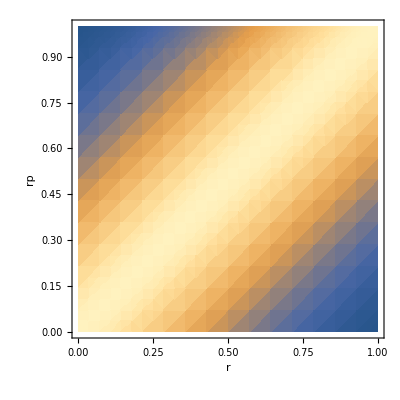

```mathematica
DensityPlot[HeavisideTheta[1-rp] E^((-(r-rp)^2)/b^2),{r,0,1},{rp,0,1},FrameLabel->{"r","rp"}]
```

#### Bessel Function Equivalence to the above

This shows that bessel function is equivalent to a solid sphere model

```mathematica
FourierTransform[BesselJ[1,q]/q,q,r]
```

√(2/π) √(1-r^2) (-1+UnitStep[-1-r]) (-1+UnitStep[-1+r])

```mathematica
Simplify[√(2/π) √(1-r^2) (-1+UnitStep[-1-r]) (-1+UnitStep[-1+r])]
```

Piecewise[{{(√(2-2 r^2))/(√π), -1<r<1}, {0, True}}]

### Atomic FFs

From: https://lampx.tugraz.at/~hadley/ss1/crystaldiffraction/atomicformfactors/formfactors.php

Units are in inverse angstrom

```mathematica
FeAFFCoeffs = <|"a"->{11.7695,7.3573,3.5222,2.3045},"b"->{4.7611,0.3072,15.3535,76.8805},"c"->1.0369,"Z"->26|>;
SiAFFCoeffs = <|"a"->{6.2915,3.0353,1.9891,1.541},"b"->{2.4386,32.3337,0.6785,81.6937},"c"->1.1407,"Z"->14|>;
MgAFFCoeffs = <|"a"->{5.4204,2.1735,1.2269,2.3073},"b"->{2.8275,79.2611,0.380,7.1937},"c"->0.8584,"Z"->12|>;
OAFFCoeffs = <|"a"->{3.0485,2.2868,1.5463,0.867},"b"->{13.2771,5.7011,0.3239,32.9089},"c"->0.2508,"Z"->8|>;
```

```mathematica
AFF[q_,coeffs_]:=Module[{},
	Sum[coeffs[["a"]][[i]] Exp[-coeffs[["b"]][[i]] (q/(4 π))^2],{i,4}]+coeffs[["c"]]
]
```

0 is slightly off from the numerical fit, so we fix Z to the value of the FFs at q=0 so that the FF vanishes there

```mathematica
FeAFFCoeffs[["Z"]]=Sum[FeAFFCoeffs[["a"]][[i]],{i,4}] + FeAFFCoeffs[["c"]];
SiAFFCoeffs[["Z"]]=Sum[SiAFFCoeffs[["a"]][[i]],{i,4}] + SiAFFCoeffs[["c"]];
MgAFFCoeffs[["Z"]]=Sum[MgAFFCoeffs[["a"]][[i]],{i,4}] + MgAFFCoeffs[["c"]];
OAFFCoeffs[["Z"]]=Sum[OAFFCoeffs[["a"]][[i]],{i,4}] + OAFFCoeffs[["c"]];
```

```mathematica
Show[{Plot[Callout[AFF[(10^6 q)/(eVm 10^10),FeAFFCoeffs],"Fe",Above],{q,0,50/10^6 10^10 eVm},AxesLabel->{"q[MeV]","F^2(q) []"}],Plot[Callout[AFF[(10^6 q)/(eVm 10^10),SiAFFCoeffs],"Si",Above],{q,0,50/10^6 10^10 eVm},PlotRange->{0,30},PlotStyle->Orange],Plot[Callout[AFF[(10^6 q)/(eVm 10^10),MgAFFCoeffs],"Mg",Above],{q,0,50/10^6 10^10 eVm},PlotRange->{0,30},PlotStyle->Green],Plot[Callout[AFF[(10^6 q)/(eVm 10^10),OAFFCoeffs],"O",Above],{q,0,50/10^6 10^10 eVm},PlotRange->{0,30},PlotStyle->Red]}]
```

-Graphics-

```mathematica
Show[{Plot[Callout[AFF[q,FeAFFCoeffs],"Fe",Above],{q,0,50},AxesLabel->{"q[Å^-1]","F^2(q) []"}],Plot[Callout[AFF[q,SiAFFCoeffs],"Si",Above],{q,0,50},PlotRange->{0,30},PlotStyle->Orange],Plot[Callout[AFF[q,MgAFFCoeffs],"Mg",Above],{q,0,50},PlotRange->{0,30},PlotStyle->Green],Plot[Callout[AFF[q,OAFFCoeffs],"O",Above],{q,0,50},PlotRange->{0,30},PlotStyle->Red]}]
```

-Graphics-

```mathematica
Show[{Plot[Callout[FeAFFCoeffs[["Z"]]-AFF[(10^6 q)/(eVm 10^10),FeAFFCoeffs],"Fe",Above],{q,0,50/10^6 10^10 eVm},AxesLabel->{"q[MeV]","Z^2(q) []"}],Plot[Callout[SiAFFCoeffs[["Z"]]-AFF[(10^6 q)/(eVm 10^10),SiAFFCoeffs],"Si",Above],{q,0,50/10^6 10^10 eVm},PlotRange->{0,30},PlotStyle->Orange],Plot[Callout[MgAFFCoeffs[["Z"]]-AFF[(10^6 q)/(eVm 10^10),MgAFFCoeffs],"Mg",Above],{q,0,50/10^6 10^10 eVm},PlotRange->{0,30},PlotStyle->Green],Plot[Callout[OAFFCoeffs[["Z"]]-AFF[(10^6 q)/(eVm 10^10),OAFFCoeffs],"O",Above],{q,0,50/10^6 10^10 eVm},PlotRange->{0,30},PlotStyle->Red]}]
```

-Graphics-

```mathematica
Show[{Plot[Callout[FeAFFCoeffs[["Z"]]-AFF[q,FeAFFCoeffs],"Fe",Above],{q,0,50},AxesLabel->{"q[Å^-1]","Z^2(q) []"}],Plot[Callout[SiAFFCoeffs[["Z"]]-AFF[q,SiAFFCoeffs],"Si",Above],{q,0,50 },PlotRange->{0,30},PlotStyle->Orange],Plot[Callout[MgAFFCoeffs[["Z"]]-AFF[q,MgAFFCoeffs],"Mg",Above],{q,0,50},PlotRange->{0,30},PlotStyle->Green],Plot[Callout[OAFFCoeffs[["Z"]]-AFF[q,OAFFCoeffs],"O",Above],{q,0,50},PlotRange->{0,30},PlotStyle->Red]}]
```

-Graphics-

```mathematica
Show[{LogLogPlot[Callout[(FeAFFCoeffs[["Z"]]-AFF[q 10^5,FeAFFCoeffs])1/MaxFe N[(3 BesselJ[1,q rnFe]/(q rnFe))^2 E^(-(q s)^2)],"Fe",Below],{q,10^-7,10 },PlotRange->{10^-7,30},AxesLabel->{"q[fm^-1]","Z^2(q) []"}],LogLogPlot[Callout[(SiAFFCoeffs[["Z"]]-AFF[q 10^5,SiAFFCoeffs])1/MaxSi N[(3 BesselJ[1,q rnSi]/(q rnSi))^2 E^(-(q s)^2)],"Si"],{q,10^-7,10 },PlotStyle->Orange],LogLogPlot[Callout[(MgAFFCoeffs[["Z"]]-AFF[q 10^5,MgAFFCoeffs])1/MaxMg N[(3 BesselJ[1,q rnMg]/(q rnMg))^2 E^(-(q s)^2)],"Mg",Below],{q,10^-7,10 },PlotStyle->Green],LogLogPlot[Callout[(OAFFCoeffs[["Z"]]-AFF[q 10^5,OAFFCoeffs])1/MaxO N[(3 BesselJ[1,q rnO]/(q rnO))^2 E^(-(q s)^2)],"O",Below],{q,10^-7,10 },PlotStyle->Red]}]
```

-Graphics-

```mathematica
eVm = 1.2 10^(-6); (*[eV m]*)
```

```mathematica
eVm 10^10
eVm 10^15
```

12000.

1.2×10^9

```mathematica
Show[{LogLogPlot[Callout[(FeAFFCoeffs[["Z"]]-AFF[q/(eVm 10^15) 10^5,FeAFFCoeffs])1/MaxFe N[3 BesselJ[1,q/(eVm 10^15) rnFe]/(q/(eVm 10^15) rnFe)E^((-(q/(eVm 10^15) s)^2)/2)],"Fe",Below],{q,10^-7 eVm 10^15,10 eVm 10^15 },PlotRange->{10^-7,30},AxesLabel->{"q[eV]","Z(q) []"}],LogLogPlot[Callout[(SiAFFCoeffs[["Z"]]-AFF[q/(eVm 10^15) 10^5,SiAFFCoeffs])1/MaxSi N[3 BesselJ[1,q/(eVm 10^15) rnSi]/(q/(eVm 10^15) rnSi)E^((-(q/(eVm 10^15) s)^2)/2)],"Si"],{q,10^-7 eVm 10^15,10 eVm 10^15 },PlotStyle->Orange],LogLogPlot[Callout[(MgAFFCoeffs[["Z"]]-AFF[q/(eVm 10^15) 10^5,MgAFFCoeffs])1/MaxMg N[3 BesselJ[1,q/(eVm 10^15) rnMg]/(q/(eVm 10^15) rnMg)E^((-(q/(eVm 10^15) s)^2)/2)],"Mg",Below],{q,10^-7 eVm 10^15,10 eVm 10^15 },PlotStyle->Green],LogLogPlot[Callout[(OAFFCoeffs[["Z"]]-AFF[q/(eVm 10^15) 10^5,OAFFCoeffs])1/MaxO N[3 BesselJ[1,q/(eVm 10^15) rnO]/(q/(eVm 10^15) rnO)E^((-(q/(eVm 10^15) s)^2)/2)],"O",Below],{q,10^-7 eVm 10^15,10 eVm 10^15 },PlotStyle->Red]}]
```

-Graphics-

```mathematica
?Zeff
```

```mathematica
Zeff[(10^12 eVm 10^15)/(eVm 10^15),FeNucCoeffs]
```

General::munfl: Exp[-972.272] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4868.51] is too small to represent as a normalized machine number; precision may be lost.

37.4301

```mathematica
SIConstRepl
```

{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,G→6.67×10^-11}

```mathematica
10^12 eVm
```

1.2×10^6

```mathematica
"eVm"/.SIConstRepl
```

eVm

```mathematica
eVm
```

1.2×10^-6

```mathematica
10^-7 eVm 10^9 (*10^-7/m m GeV*)
```

0.00012

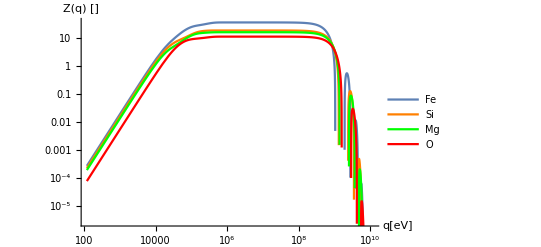

```mathematica
Show[{LogLogPlot[Zeff[q/eVm,FeNucCoeffs],{q,10^-7 eVm 10^15,10 eVm 10^15 },AxesLabel->{"q[eV]","Z(q) []"},PlotLegends->{"Fe"}],LogLogPlot[Zeff[q/eVm,SiNucCoeffs],{q,10^-7 eVm 10^15,10 eVm 10^15 },PlotStyle->Orange,PlotLegends->{"Si"}],LogLogPlot[Zeff[q/eVm,MgNucCoeffs],{q,10^-7 eVm 10^15,10 eVm 10^15 },PlotStyle->Green,PlotLegends->{"Mg"}],LogLogPlot[Zeff[q/eVm,ONucCoeffs],{q,10^-7 eVm 10^15,10 eVm 10^15 },PlotStyle->Red,PlotLegends->{"O"}]}]
```

```mathematica
Show[{LogLogPlot[Callout[((FeAFFCoeffs[["Z"]]-AFF[q/(eVm 10^15) 10^5,FeAFFCoeffs])1/MaxFe N[3 BesselJ[1,q/(eVm 10^15) rnFe]/(q/(eVm 10^15) rnFe)E^((-(q/(eVm 10^15) s)^2)/2)])^2,"Fe",Below],{q,10^-7 eVm 10^15,10 eVm 10^15 },PlotRange->{10^-7,30},AxesLabel->{"q[eV]","Z^2(q) []"}],LogLogPlot[Callout[((SiAFFCoeffs[["Z"]]-AFF[q/(eVm 10^15) 10^5,SiAFFCoeffs])1/MaxSi N[3 BesselJ[1,q/(eVm 10^15) rnSi]/(q/(eVm 10^15) rnSi)E^((-(q/(eVm 10^15) s)^2)/2)])^2,"Si"],{q,10^-7 eVm 10^15,10 eVm 10^15 },PlotStyle->Orange],LogLogPlot[Callout[((MgAFFCoeffs[["Z"]]-AFF[q/(eVm 10^15) 10^5,MgAFFCoeffs])1/MaxMg N[3 BesselJ[1,q/(eVm 10^15) rnMg]/(q/(eVm 10^15) rnMg)E^((-(q/(eVm 10^15) s)^2)/2)])^2,"Mg",Below],{q,10^-7 eVm 10^15,10 eVm 10^15 },PlotStyle->Green],LogLogPlot[Callout[((OAFFCoeffs[["Z"]]-AFF[q/(eVm 10^15) 10^5,OAFFCoeffs])1/MaxO N[3 BesselJ[1,q/(eVm 10^15) rnO]/(q/(eVm 10^15) rnO)E^((-(q/(eVm 10^15) s)^2)/2)])^2,"O",Below],{q,10^-7 eVm 10^15,10 eVm 10^15 },PlotStyle->Red]}]
```

-Graphics-

Adjust / correctnuclear FFs -

```mathematica
Show[{Plot[Callout[FeAFFCoeffs[["Z"]]-√AFF[(10^6 q)/(eVm 10^10),FeAFFCoeffs],"Fe",Above],{q,0,50/10^6 10^10 eVm},PlotRange->{0,30},AxesLabel->{"q[MeV]","Z(q) []"}],Plot[Callout[SiAFFCoeffs[["Z"]]-√AFF[(10^6 q)/(eVm 10^10),SiAFFCoeffs],"Si",Above],{q,0,50/10^6 10^10 eVm},PlotRange->{0,30},PlotStyle->Orange],Plot[Callout[MgAFFCoeffs[["Z"]]-√AFF[(10^6 q)/(eVm 10^10),MgAFFCoeffs],"Mg",Above],{q,0,50/10^6 10^10 eVm},PlotRange->{0,30},PlotStyle->Green],Plot[Callout[OAFFCoeffs[["Z"]]-√AFF[(10^6 q)/(eVm 10^10),OAFFCoeffs],"O",Above],{q,0,50/10^6 10^10 eVm},PlotRange->{0,30},PlotStyle->Red]}]
```

-Graphics-

Nope, all good it was right

#### Test package

```mathematica
SiCoeffs
```

<|a→{6.2915,3.0353,1.9891,1.541},b→{2.4386,32.3337,0.6785,81.6937},c→1.1407,Z→13.9976,A→28,rn→3.46171|>

```mathematica
eVm = 1.2 10^(-6); (*[eV m]*)
```

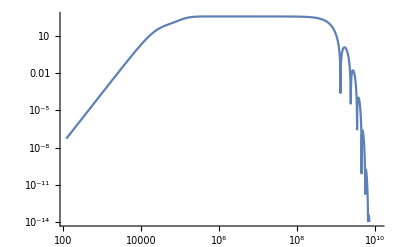

```mathematica
LogLogPlot[Zeff[q/(eVm 10^15) 10^5,SiCoeffs]^2,{q,10^-7 eVm 10^15,10 eVm 10^15}]
```

```mathematica
LogLogPlot[Zeff[q/eVm,SiCoeffs]^2,{q,10^-7 eVm ,10 eVm}]
```

-Graphics-

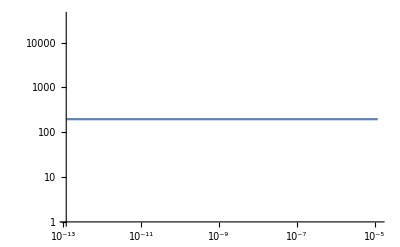

```mathematica
LogLogPlot[AFF[q/eVm,SiCoeffs]^2,{q,10^-7 eVm ,10 eVm}]
```

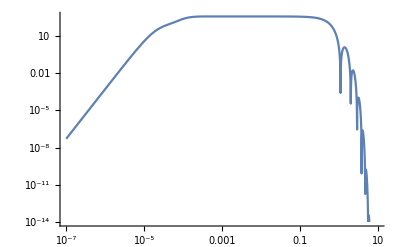

```mathematica
LogLogPlot[Zeff[q 10^5,SiCoeffs]^2,{q,10^-7 ,10}] (*ang*)
```

```mathematica
LogLogPlot[Zeff[q ,SiCoeffs]^2,{q,10^-7 ,10}] (*fm*)
```

-Graphics-

```mathematica
LogLogPlot[Zeff[q  10^15,SiCoeffs]^2,{q,10^-7  ,10 }] (* input in fm^-1, functions with m*)
```

-Graphics-

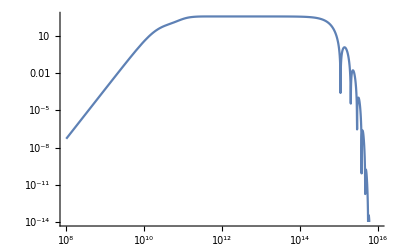

```mathematica
LogLogPlot[Zeff[q ,SiCoeffs]^2,{q,10^-7 10^15,10 10^15 }] (* input in m^-1, functions with m^-1*)
```

```mathematica
LogLogPlot[Zeff[q/eVm,SiCoeffs]^2,{q,10^-7 10^15 eVm,10 10^15 eVm }] (*input in eV, functions with m^-1*)
```

-Graphics-

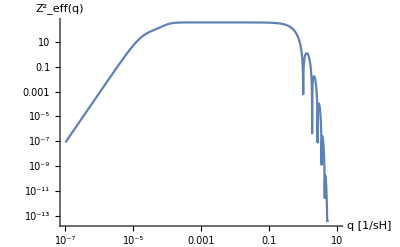

```mathematica
LogLogPlot[Zeff[q/sH,SiCoeffs]^2,{q,10^-7 ,10 },AxesLabel->{"q [1/sH]","(Z^2)_eff(q)"}] (* input in m^-1, functions with m^-1*)
```

### Compute energy loss

```mathematica
Integrate[((("e")^2/(4π "ϵ0")/.SIConstRepl)Zeff[q/sH,FeCoeffs]/q^2)^2,{q,0,∞}]
```

∫_0^∞ 1/q^6 2.04534×10^-56 ⅇ^(-1. q^2) (24.9535-2.3045 ⅇ^(-6.01051×10^9 q^2)-3.5222 ⅇ^(-1.20034×10^9 q^2)-11.7695 ⅇ^(-3.72222×10^8 q^2)-7.3573 ⅇ^(-2.40169×10^7 q^2))^2 BesselJ[1,4.84609 q]^2 ⅆq

```mathematica
NIntegrate[4 π q^2((("e")^2/(4π "ϵ0")/.SIConstRepl)Zeff[q/sH,FeCoeffs]/q^2)^2,{q,0,∞}]
```

1.57723×10^-47

### Nuclear scattering energy loss formula

#### reduce integral

```mathematica
Integrate[p E^{- a p^2},{p,0,∞}]
```

{ConditionalExpression[1/(2 a), Re[a]>0]}

```mathematica
Integrate[p E^{- a p^2},{p,b,c}]
```

{(ⅇ^(-a b^2)-ⅇ^(-a c^2))/(2 a)}

solve for bounds

```mathematica
Solve[(ℏ q p)/mn-(ℏ q^2)/(2 mn)== ω,p]
```

{{p→(2 mn ω+q^2 ℏ)/(2 q ℏ)}}

```mathematica
Solve[-((ℏ q p)/mn+(ℏ q^2)/(2 mn))== ω,p]
Simplify[(p/.%[[1]])^2]
```

{{p→(-2 mn ω-q^2 ℏ)/(2 q ℏ)}}

((2 mn ω+q^2 ℏ)^2)/(4 q^2 ℏ^2)

Evaluate p integral

```mathematica
Integrate[p E^((- β ℏ^2)/(2 mN) p^2),{p,a,b}]
```

((ⅇ^(-(a^2 β ℏ^2)/(2 mN))-ⅇ^(-(b^2 β ℏ^2)/(2 mN))) mN)/(β ℏ^2)

```mathematica
Integrate[ω^2 E^(- β (ℏ^2 (mN/(q ℏ)ω + q/2)^2)/(2 mN)),{ω,a,b}]
```

1/(8 mN^(5/2) β^(3/2))q^2 (4 ⅇ^(-(β (2 a mN+q^2 ℏ)^2)/(8 mN q^2)) √mN √β (2 a mN-q^2 ℏ)+4 ⅇ^(-(β (2 b mN+q^2 ℏ)^2)/(8 mN q^2)) √mN √β (-2 b mN+q^2 ℏ)-√(2 π) q (4 mN+q^2 β ℏ^2) Erf[(√β (2 a mN+q^2 ℏ))/(2 √2 √mN q)]+√(2 π) q (4 mN+q^2 β ℏ^2) Erf[(√β (2 b mN+q^2 ℏ))/(2 √2 √mN q)])

```mathematica
Integrate[ω^2 E^(- (c ω + d)^2),ω]
```

(2 ⅇ^(-(d+c ω)^2) (d-c ω)+(1+2 d^2) √π Erf[d+c ω])/(4 c^3)

```mathematica
Simplify[(mN ω)/(q ℏ) - q/2/.ω ->q v - (ℏ q^2)/(2mχ)]
```

-((mN+mχ) q)/(2 mχ)+(mN v)/ℏ

plug in variables explicitly

```mathematica
Integrate[p E^((- β ℏ^2)/(2 mN) p^2),{p,(mN ω)/(q ℏ) - q/2,-((mN ω)/(q ℏ) + q/2)}]
Integrate[ω  % ,{ω,-(q v + (ℏ q^2)/(2mχ)),(q v - (ℏ q^2)/(2mχ))}]
```

(ⅇ^(-(β (2 mN ω+q^2 ℏ)^2)/(8 mN q^2)) (-1+ⅇ^(β ω ℏ)) mN)/(β ℏ^2)

1/(4 √mN β^2 ℏ^2)q^2 (-4 (ⅇ^(-(β (2 mN mχ v+mN q ℏ-mχ q ℏ)^2)/(8 mN mχ^2))-ⅇ^(-(β (2 mN mχ v-mN q ℏ+mχ q ℏ)^2)/(8 mN mχ^2))) √mN+4 (-ⅇ^(-(β (-2 mN mχ v+mN q ℏ+mχ q ℏ)^2)/(8 mN mχ^2))+ⅇ^(-(β (2 mN mχ v+mN q ℏ+mχ q ℏ)^2)/(8 mN mχ^2))) √mN+√(2 π) q √β ℏ Erf[(√β (2 mN mχ v+mN q ℏ-mχ q ℏ))/(2 √2 √mN mχ)]+√(2 π) q √β ℏ Erf[(√β (2 mN mχ v-mN q ℏ+mχ q ℏ))/(2 √2 √mN mχ)]-√(2 π) q √β ℏ Erf[(√β (-2 mN mχ v+mN q ℏ+mχ q ℏ))/(2 √2 √mN mχ)]+√(2 π) q √β ℏ Erf[(√β (2 mN mχ v+mN q ℏ+mχ q ℏ))/(2 √2 √mN mχ)])

```mathematica
Integrate[p E^((- β ℏ^2)/(2 mN) p^2),{p,(mN ω)/(q ℏ) - q/2,-((mN ω)/(q ℏ) + q/2)}]
Simplify[√(mN β) Integrate[ω  % ,{ω,-(q v + (ℏ q^2)/(2mχ)),(q v - (ℏ q^2)/(2mχ))}]]
```

(ⅇ^(-(β (2 mN ω+q^2 ℏ)^2)/(8 mN q^2)) (-1+ⅇ^(β ω ℏ)) mN)/(β ℏ^2)

1/(4 √mN β^2 ℏ^2)q^2 √(mN β) (-4 (ⅇ^(-(β (2 mN mχ v+mN q ℏ-mχ q ℏ)^2)/(8 mN mχ^2))-ⅇ^(-(β (2 mN mχ v-mN q ℏ+mχ q ℏ)^2)/(8 mN mχ^2))) √mN+4 (-ⅇ^(-(β (-2 mN mχ v+mN q ℏ+mχ q ℏ)^2)/(8 mN mχ^2))+ⅇ^(-(β (2 mN mχ v+mN q ℏ+mχ q ℏ)^2)/(8 mN mχ^2))) √mN+√(2 π) q √β ℏ Erf[(√β (2 mN mχ v+mN q ℏ-mχ q ℏ))/(2 √2 √mN mχ)]+√(2 π) q √β ℏ Erf[(√β (2 mN mχ v-mN q ℏ+mχ q ℏ))/(2 √2 √mN mχ)]-√(2 π) q √β ℏ Erf[(√β (-2 mN mχ v+mN q ℏ+mχ q ℏ))/(2 √2 √mN mχ)]+√(2 π) q √β ℏ Erf[(√β (2 mN mχ v+mN q ℏ+mχ q ℏ))/(2 √2 √mN mχ)])

Can we assume that temperature is large compared to the energy transfer? if so then we get instead

```mathematica
degnucint = Integrate[ω^2 (ⅇ^(-(β (2 mN ω+q^2 ℏ)^2)/(8 mN q^2))  mN)/ℏ,{ω,-(q v + (ℏ q^2)/(2mχ)),(q v - (ℏ q^2)/(2mχ))}]
```

1/(8 mN^(3/2) mχ β^(3/2) ℏ)q^3 (4 ⅇ^(-(β (2 mN mχ v-mN q ℏ+mχ q ℏ)^2)/(8 mN mχ^2)) √mN √β (-2 mN mχ v+mN q ℏ+mχ q ℏ)-4 ⅇ^(-(β (2 mN mχ v+mN q ℏ-mχ q ℏ)^2)/(8 mN mχ^2)) √mN √β (2 mN mχ v+mN q ℏ+mχ q ℏ)+mχ √(2 π) (4 mN+q^2 β ℏ^2) Erf[(√β (2 mN mχ v+mN q ℏ-mχ q ℏ))/(2 √2 √mN mχ)]+mχ √(2 π) (4 mN+q^2 β ℏ^2) Erf[(√β (2 mN mχ v-mN q ℏ+mχ q ℏ))/(2 √2 √mN mχ)])

```mathematica
Simplify[degnucint/(4mN mχ)]
```

1/(32 mN^(5/2) mχ^2 β^(3/2) ℏ)q^3 (4 ⅇ^(-(β (2 mN mχ v-mN q ℏ+mχ q ℏ)^2)/(8 mN mχ^2)) √mN √β (-2 mN mχ v+mN q ℏ+mχ q ℏ)-4 ⅇ^(-(β (2 mN mχ v+mN q ℏ-mχ q ℏ)^2)/(8 mN mχ^2)) √mN √β (2 mN mχ v+mN q ℏ+mχ q ℏ)+mχ √(2 π) (4 mN+q^2 β ℏ^2) Erf[(√β (2 mN mχ v+mN q ℏ-mχ q ℏ))/(2 √2 √mN mχ)]+mχ √(2 π) (4 mN+q^2 β ℏ^2) Erf[(√β (2 mN mχ v-mN q ℏ+mχ q ℏ))/(2 √2 √mN mχ)])

```mathematica
<|"+"->1,"-"->(-1)|>[["-"]]
```

-1

```mathematica
SNuc[q,ω,FeCoeffs]
```

1/q^3 1.18594×10^30 √(mN β) ⅇ^(-8.1×10^-31 q^2) (24.9535-2.3045 ⅇ^(-4.86851×10^-21 q^2)-3.5222 ⅇ^(-9.72272×10^-22 q^2)-11.7695 ⅇ^(-3.015×10^-22 q^2)-7.3573 ⅇ^(-1.94537×10^-23 q^2))^2 (ⅇ^(-(β ℏ^2 (-q/2-(mN ω)/(ℏ q))^2)/(2 mN))-ⅇ^(-(β ℏ^2 (q/2-(mN ω)/(ℏ q))^2)/(2 mN))) BesselJ[1,4.36148×10^-15 q]^2

#### Unit testing for energy loss

```mathematica
SNuc[10^13,ω,"β"/.SIcrustparams,FeCoeffs]/.SIConstRepl
```

General::munfl: Exp[-30150.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1945.37] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-97227.2] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-1.69101×10^-12 (ⅇ^(-1.49481×10^-23 (-5000000000000-0.0000881137 ω)^2)-ⅇ^(-1.49481×10^-23 (5000000000000-0.0000881137 ω)^2))

```mathematica
ωIntegralNuc[10^10,10^-27,("c")/10^4/.SIConstRepl,"β"/.SIcrustparams,FeNucCoeffs,SIConstRepl]
```

3.99735×10^12

```mathematica
ωIntegralNuc[10^10,10^-27,("c")/10^2/.SIConstRepl,"β"/.SIcrustparams,FeNucCoeffs,SIConstRepl]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
ωIntegralNuc[10^14,10^-27,("c")/10^4/.SIConstRepl,"β"/.SIcrustparams,FeNucCoeffs,SIConstRepl]
```

General::munfl: Exp[-3.015×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-194537.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.72272×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
1/("JpereV")ELIntegralNuc[10^-25,("c")/10^4/.SIConstRepl,"β"/.SIcrustparams,FeNucCoeffs,SIConstRepl]/.SIConstRepl
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {1.34448×10^13}. NIntegrate obtained 1.62329×10^-68 and 2.4208×10^-70 for the integral and error estimates.

1.01329×10^-49

```mathematica
q/vχ^2 VCoul[q,params]^2/(2 π)^2/.{q->10^10,vχ->("c")/10^4/.SIConstRepl,params->SIConstRepl}
```

ReplaceAll::reps: {params} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

2.37205×10^-94

```mathematica
SIcrustparams
FeNucCoeffs
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→6.72901×10^29,qF→2.71097×10^10,vF→3.13948×10^6,μ→4.48957×10^-18,ωp→4.63071×10^16,α→1/137,χ→0.47119,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1121.02,nI→8.41126×10^28,Z→8,M→9.27329×10^-26,EF→4.48957×10^-18}

<|a→{11.7695,7.3573,3.5222,2.3045},b→{4.7611,0.3072,15.3535,76.8805},c→1.0369,Z→25.9904,A→56,rn→4.36148×10^-15,mN→9.296×10^-26|>

```mathematica
VCoul[q,params]/.{q->10^11,vχ->("c")/10^4/.SIConstRepl,params->SIConstRepl}
```

ReplaceAll::reps: {params} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

2.90311×10^-49

```mathematica
("e")^2/("ϵ0")/.SIConstRepl
("β"("ℏ")^2)/("mN")/.SIcrustparams /. FeNucCoeffs
```

2.90311×10^-27

2.98963×10^-23

```mathematica
1/("JpereV")ELIntegralNuc[10^-25,("c")/10^4/.SIConstRepl,"β"/.SIcrustparams,FeNucCoeffs,SIConstRepl]/.SIConstRepl
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {1.34448×10^13}. NIntegrate obtained 1.62329×10^-68 and 2.4208×10^-70 for the integral and error estimates.

1.01329×10^-49

```mathematica
Integrate[DiracDelta[(ℏ^2 q^2)/(2 mN)-(ℏ^2 p u q)/(2 mN)-ℏ ω],{u,-1,1}]
```

(2 mN (HeavisideTheta[(ℏ (2 mN ω+(p-q) q ℏ))/mN]-HeavisideTheta[ℏ (2 ω-(q (p+q) ℏ)/mN)]))/(p q ℏ^2)

#### 0 Temperature approach

```mathematica
Integrate[ω DiracDelta[(ℏ^2 q^2)/(2 mN)-ℏ ω],{ω,a,b}]
```

ConditionalExpression[(q^2 Boole[a<(q^2 ℏ)/(2 mN)<b||b<(q^2 ℏ)/(2 mN)<a] Sign[ℏ])/(2 mN), ]

```mathematica
ELIntegralNuc0[10^-23,("c")/10^2/.SIConstRepl,FeNucCoeffs,SIConstRepl]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {9.42192×10^10}. NIntegrate obtained 5.12656×10^-25 and 6.96094×10^-31 for the integral and error estimates.

9.56436×10^-73

```mathematica
("ℏ" vχ)/(2 (("mN")^-1+mχ^-1)^-1)/. SIConstRepl /.FeNucCoeffs
```

5.275×10^-35 (1.07573×10^25+1/mχ) vχ

```mathematica
q^3/(2("mN"/. FeNucCoeffs))VCoul[q,SIConstRepl]^2 Zeff[q,FormFactors`FeNucCoeffs]^2
```

1/q^3 21.4474 ⅇ^(-8.1×10^-31 q^2) (24.9535-2.3045 ⅇ^(-4.86851×10^-21 q^2)-3.5222 ⅇ^(-9.72272×10^-22 q^2)-11.7695 ⅇ^(-3.015×10^-22 q^2)-7.3573 ⅇ^(-1.94537×10^-23 q^2))^2 BesselJ[1,4.36148×10^-15 q]^2

```mathematica
(2 (("mN")^-1+mχ^-1)^-1 vχ)/("ℏ")/. SIConstRepl /.FormFactors`FeNucCoeffs/.mχ->10^-23/.vχ->("c")/10^2/.SIConstRepl
```

5.23813×10^15

#### Comparison finite temp and 0 temp

```mathematica
(1/("JpereV")/.SIConstRepl)ELIntegralNuc[10^-26,("c")/10^4/.SIConstRepl,"β"/.SIcrustparams,FeNucCoeffs,SIConstRepl]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {3.00485×10^12}. NIntegrate obtained 9.3455×10^-35 and 2.50872×10^-38 for the integral and error estimates.

5.83364×10^-16

```mathematica
(1/("JpereV")/.SIConstRepl)("nI"/.SIcrustparams)ELIntegralNuc0[10^-31,("c")/10^4/.SIConstRepl,FeNucCoeffs,SIConstRepl]
```

8.32687

```mathematica
(1/("JpereV")/.SIConstRepl)("nI"/.SIcrustparams)ELIntegralNuc[10^-31,("c")/10^4/.SIConstRepl,1000"β"/.SIcrustparams,FeNucCoeffs,SIConstRepl]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {874815.}. NIntegrate obtained 1.40739×10^-54 and 2.85899×10^-55 for the integral and error estimates.

7.38947×10^-7

```mathematica
("nI"/.SIcrustparams)
```

8.41126×10^28

#### Test new modules and format

```mathematica
EnergyLossNuc0[10^-31,("c")/10^4/.SIConstRepl,FeNucCoeffs,SIConstRepl,<|"nI"->("nI"/.SIcrustparams)|>]
```

For mχ = 1.×10^-31 , vχ = 30000
dEdr:	8.32687

<|mχ→1.×10^-31,vχ→30000,params→{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23},coeffs→<|a→{11.7695,7.3573,3.5222,2.3045},b→{4.7611,0.3072,15.3535,76.8805},c→1.0369,Z→25.9904,A→56,rn→4.36148×10^-15,mN→9.296×10^-26|>,statpars→<|nI→8.41126×10^28|>,dEdr→8.32687|>

```mathematica
Information[ELIntegralNuc]
```

```mathematica
(1/("JpereV")/.SIConstRepl)ELIntegralNuc[10^-31, ("c")/10^4/.SIConstRepl,FeNucCoeffs,SIConstRepl,<|"nI"->("nI"/.SIcrustparams),"β"->(1000βcrust)|>]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {874815.}. NIntegrate obtained 1.40739×10^-54 and 2.85899×10^-55 for the integral and error estimates.

7.38947×10^-7

```mathematica
EnergyLossNuc[10^-31,("c")/10^4/.SIConstRepl,FeNucCoeffs,SIConstRepl,<|"nI"->("nI"/.SIcrustparams),"β"->(βcrust)|>]
```

For mχ = 1.×10^-31 , vχ = 30000
dEdr:	11.9143

<|mχ→1.×10^-31,vχ→30000,params→{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23},coeffs→<|a→{11.7695,7.3573,3.5222,2.3045},b→{4.7611,0.3072,15.3535,76.8805},c→1.0369,Z→25.9904,A→56,rn→4.36148×10^-15,mN→9.296×10^-26|>,statpars→<|nI→8.41126×10^28,β→2.49694×10^20|>,dEdr→11.9143|>

```mathematica
EnergyLossNuc[10^-31,("c")/10^4/.SIConstRepl,FeNucCoeffs,SIConstRepl,<|"nI"->("nI"/.SIcrustparams),"β"->(1000βcrust)|>]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {874815.}. NIntegrate obtained 1.40739×10^-54 and 2.85899×10^-55 for the integral and error estimates.

For mχ = 1.×10^-31 , vχ = 30000
dEdr:	7.38947×10^-7

<|mχ→1.×10^-31,vχ→30000,params→{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23},coeffs→<|a→{11.7695,7.3573,3.5222,2.3045},b→{4.7611,0.3072,15.3535,76.8805},c→1.0369,Z→25.9904,A→56,rn→4.36148×10^-15,mN→9.296×10^-26|>,statpars→<|nI→8.41126×10^28,β→2.49694×10^23|>,dEdr→7.38947×10^-7|>

#### Test Energy Loss and Interpolation

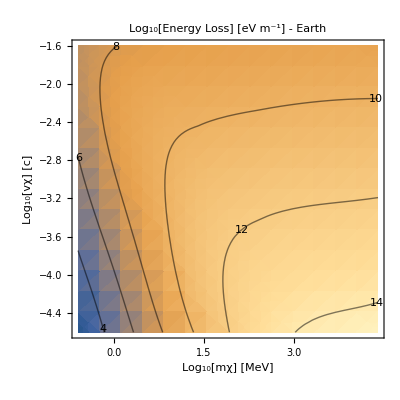

```mathematica
NucFeELDict = EnergyLossTableAndInterNuc0[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ" -> 6, "vχ" -> 4|>,FeNucCoeffs,SIConstRepl,<|"nI"->("nI"/.SIcrustparams)|>,True,"FeNuc0ELOutputDict","Fe T=0",False];
PlotEL[NucFeELDict]
```

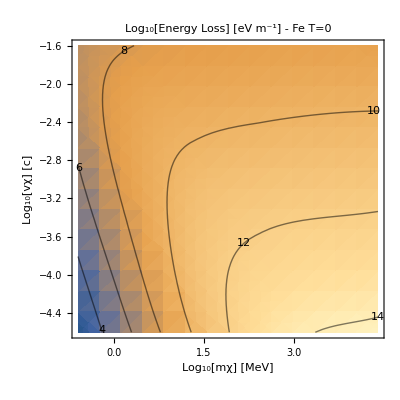

```mathematica
NucSiELDict = EnergyLossTableAndInterNuc0[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ" -> 6, "vχ" -> 4|>,SiNucCoeffs,SIConstRepl,<|"nI"->("nI"/.SIcrustparams)|>,True,"SiNuc0ELOutputDict","Si T=0",False];
PlotEL[NucSiELDict,"Fe T=0"]
```

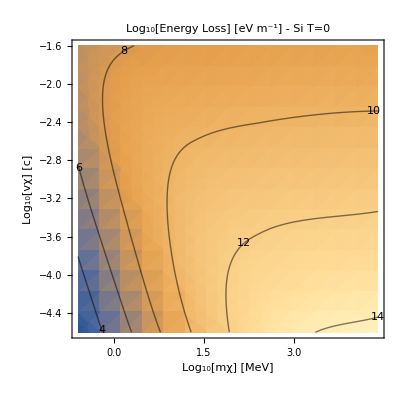

```mathematica
NucSiELDict = EnergyLossTableAndInterNuc0[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ" -> 6, "vχ" -> 4|>,SiNucCoeffs,SIConstRepl,<|"nI"->("nI"/.SIcrustparams)|>,True,"SiNuc0ELOutputDict","Si T=0",False];
PlotEL[NucSiELDict,"Si T=0"]
```

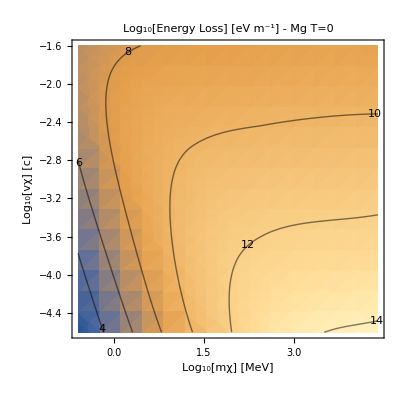

```mathematica
NucMgELDict = EnergyLossTableAndInterNuc0[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ" -> 6, "vχ" -> 4|>,MgNucCoeffs,SIConstRepl,<|"nI"->("nI"/.SIcrustparams)|>,True,"MgNuc0ELOutputDict","Mg T=0",False];
PlotEL[NucMgELDict,"Mg T=0"]
```

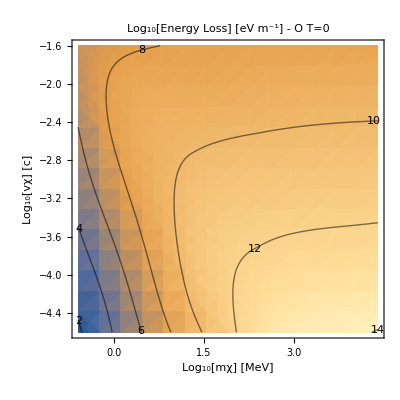

```mathematica
NucOELDict = EnergyLossTableAndInterNuc0[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ" -> 6, "vχ" -> 4|>,ONucCoeffs,SIConstRepl,<|"nI"->("nI"/.SIcrustparams)|>,True,"ONuc0ELOutputDict","O T=0",False];
PlotEL[NucOELDict,"O T=0"]
```

```mathematica
"mN"/.FeNucCoeffs
%/("JpereV")/.SIConstRepl
% ("c")^2/.SIConstRepl
```

9.296×10^-26

5.80275×10^-7

5.22247×10^10